```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tep/Dropbox/Mon Mac (MBP-de-admin)/Documents/tex_bulge/code/nb

```mathematica
lenA=1
(*Import["../data/Dump_Eigenmode.hf5",{"Datasets","a"}]*)
lenC=1/10(*Import["../data/Dump_Eigenmode.hf5",{"Datasets","c"}]*)
r=lenA/lenC
x=0
(*Import["../data/Dump_Eigenmode.hf5",{"Datasets","x"}]*)
q=1(*Import["../data/Dump_Eigenmode.hf5",{"Datasets","q"}]*)
m=Import["../data/Dump_Eigenmode.hf5",{"Datasets","m"}]
ϵ=0.1(*Import["../data/Dump_Eigenmode.hf5",{"Datasets","eps"}]*)
egv=Import["../data/Dump_Eigenmode.hf5",{"Datasets","egv"}]
tabaln=Import["../data/Dump_Eigenmode.hf5",{"Datasets","aln"}];
nb=Length[tabaln]
tabaln=Table[tabaln[[i]][[1]]+I*tabaln[[i]][[2]],{i,1,nb}];
```

1

1/10

10

0

1

2

0.1

<|r→1.59892,i→1.06707|>

121

```mathematica
precRate=egv[[1]]
radc2[ξ_]:=(r)^2*(1+ξ)/(1-ξ);
rad[ξ_]:=(1+ξ)/(1-ξ);
Omega[ξ_]:=((1-ξ)/2)^(3/4)*Sqrt[(r)^3*(x)/(1-x)((1-ξ)/2)^(-3/2)*(1/(1+radc2[ξ]))^(3/2)+1/q-ϵ*(1/((1-x)^(2/3)))]\Sqrt[1-x]
xi[rd_]:=(rd^2-lenA^2)/(rd^2+lenA^2)
radius[x_,y_]:=Sqrt[x^2+y^2]
angle[x_,y_]:=ArcTan[x,y]
NLegendre[n_,m_,x_]:=Sqrt[Factorial[n-m]*(2n+1)/(2*Factorial[n+m])]*LegendreP[n,m,x]
Density[x_,y_]:=Re[((1-xi[radius[x,y]])/2)^(3/2)*Sum[tabaln[[i]]*NLegendre[m+i-1,m,xi[radius[x,y]]]*E^(I*m*angle[x,y]),{i,1,nb}]]
```

1.59892

```mathematica
domegadxi[ξ_]:=-((3 ((-1+x+q (1-x)^(1/3) ϵ) (1-ξ)^(5/2)+r^4 (-1+x+q (1-x)^(1/3) ϵ) √(1-ξ) (1+ξ)^2-2 r^2 (-1+x+q (1-x)^(1/3) ϵ) √(1-ξ) (-1+ξ^2)-4 q r^5 x √((2-2 ξ)/(1-ξ+r^2 (1+ξ)))))/(4 q (-1+x) (2-2 ξ)^(3/4) (1-ξ+r^2 (1+ξ))^2 √(1/q-ϵ/(1-x)^(2/3)-(r^3 x ((2-2 ξ)/(1-ξ+r^2 (1+ξ)))^(3/2))/((-1+x) (1-ξ)^(3/2)))))
kappa2[ξ_]:=4*Omega[ξ]^2*(1+((1+ξ)(1-ξ))/(2*Omega[ξ])*domegadxi[ξ])
kappa[ξ_]:=Sqrt[kappa2[ξ]]
```

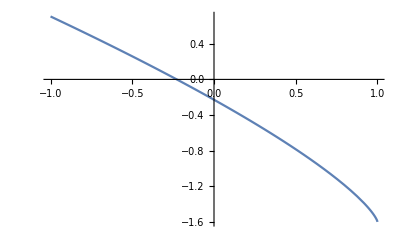

```mathematica
Plot[m*Omega[ξ]-precRate,{ξ,-1,1}]
```

```mathematica
1/(precRate^(1/3))
```

0.855181

```mathematica
(*eps=0.15*)
```

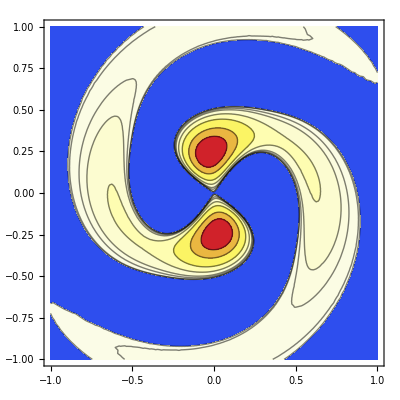

```mathematica
rmax=1;
contours={1.5,1,0.5,0.25,0.1,0.05,0.01,0.005}(*10^{0,-1,-2,-3,-4}*);
pCt=ContourPlot[Density[x,y],{x,-rmax,rmax},{y,-rmax,rmax},PlotRange->{All,All,All},Contours->contours,ColorFunction->"TemperatureMap"]
```

{-0.227913}

0.628779

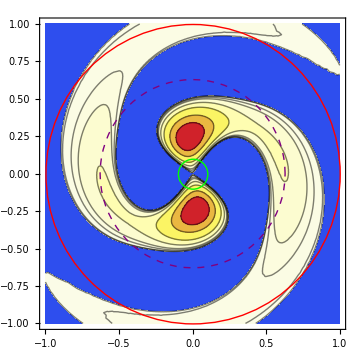

```mathematica
ξc=ξc/.NSolve[m*Omega[ξc]-precRate,ξc,Reals]
rc=rad[ξc[[1]]]
regA=Graphics[{Red,Thick,Circle[{0,0},lenA]}];
regCr=Graphics[{Purple,Thick,Dashed,Circle[{0,0},rc]}];
regC=Graphics[{Green,Thick,Circle[{0,0},lenC]}];
Show[pCt,regA,regCr,regC,ImageSize->Medium]
```